```mathematica
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"UTILITY_readBeamFiles.nb"}]]
```

```mathematica
fileNames = FileNames["~/tmpSLACData/*h5"]
```

{~/tmpSLACData/1026799966932734004_PENT.h5,~/tmpSLACData/103749140491903505_PENT.h5,~/tmpSLACData/1085244394845391034_PENT.h5,~/tmpSLACData/1133836135064138554_PENT.h5,~/tmpSLACData/1135313060239920135_PENT.h5,~/tmpSLACData/1153711681517519558_PENT.h5,~/tmpSLACData/1220208668776450780_PENT.h5,~/tmpSLACData/1273508207329436594_PENT.h5,~/tmpSLACData/1367015535428430260_PENT.h5,~/tmpSLACData/1395739019504530692_PENT.h5,~/tmpSLACData/1411202764023273851_PENT.h5,~/tmpSLACData/1421474545032375180_PENT.h5,~/tmpSLACData/1479575759690492241_PENT.h5,~/tmpSLACData/1483891030905655908_PENT.h5,~/tmpSLACData/1503131240646430108_PENT.h5,~/tmpSLACData/1586288883651975774_PENT.h5,~/tmpSLACData/1613994990981693360_PENT.h5,~/tmpSLACData/1751450444192141885_PENT.h5,~/tmpSLACData/1815757477989188641_PENT.h5,~/tmpSLACData/1839797423727388323_PENT.h5,~/tmpSLACData/1984630376617872887_PENT.h5,~/tmpSLACData/2008737860570883320_PENT.h5,~/tmpSLACData/2013033130008149274_PENT.h5,~/tmpSLACData/2024219766133681193_PENT.h5,~/tmpSLACData/2053701066988875905_PENT.h5,~/tmpSLACData/2137604631446762044_PENT.h5,~/tmpSLACData/2276649386895281994_PENT.h5,~/tmpSLACData/2276729237227534312_PENT.h5,~/tmpSLACData/2303889797970960652_PENT.h5,~/tmpSLACData/2319329469030025314_PENT.h5,~/tmpSLACData/2354331844451573920_PENT.h5,~/tmpSLACData/2368180293970906893_PENT.h5,~/tmpSLACData/2385742590165990511_PENT.h5,~/tmpSLACData/2493658735016631454_PENT.h5,~/tmpSLACData/2501434899129669097_PENT.h5,~/tmpSLACData/2505464849343316053_PENT.h5,~/tmpSLACData/2580960583022949167_PENT.h5,~/tmpSLACData/2734946681722051078_PENT.h5,~/tmpSLACData/2735799535565430277_PENT.h5,~/tmpSLACData/2784436957319843903_PENT.h5,~/tmpSLACData/281581192420883394_PENT.h5,~/tmpSLACData/2840997012627403153_PENT.h5,~/tmpSLACData/285316600481598365_PENT.h5,~/tmpSLACData/2875991919748621984_PENT.h5,~/tmpSLACData/2910268202137441960_PENT.h5,~/tmpSLACData/2937764455492501449_PENT.h5,~/tmpSLACData/3004852522657811525_PENT.h5,~/tmpSLACData/3017004914615208537_PENT.h5,~/tmpSLACData/3131687835279105367_PENT.h5,~/tmpSLACData/3152471567442935589_PENT.h5,~/tmpSLACData/3155168262180907274_PENT.h5,~/tmpSLACData/3180554906241751237_PENT.h5,~/tmpSLACData/3191034885121359203_PENT.h5,~/tmpSLACData/3211069982733633199_PENT.h5,~/tmpSLACData/3300513869037558101_PENT.h5,~/tmpSLACData/3321277431330308065_PENT.h5,~/tmpSLACData/3334148631261998637_PENT.h5,~/tmpSLACData/3350548750110223508_PENT.h5,~/tmpSLACData/3443560842265842562_PENT.h5,~/tmpSLACData/3459491238518120177_PENT.h5,~/tmpSLACData/3532772539754912219_PENT.h5,~/tmpSLACData/360368292420609113_PENT.h5,~/tmpSLACData/3661601783775130884_PENT.h5,~/tmpSLACData/3833512618963444434_PENT.h5,~/tmpSLACData/3853996069261158242_PENT.h5,~/tmpSLACData/3944996454768139250_PENT.h5,~/tmpSLACData/3966823547137373865_PENT.h5,~/tmpSLACData/4000380211719351475_PENT.h5,~/tmpSLACData/4197080386518031410_PENT.h5,~/tmpSLACData/4208146379186719770_PENT.h5,~/tmpSLACData/4267160164234117289_PENT.h5,~/tmpSLACData/4411709827444950356_PENT.h5,~/tmpSLACData/4426743639426606883_PENT.h5,~/tmpSLACData/4432945792665575150_PENT.h5,~/tmpSLACData/445246833458401474_PENT.h5,~/tmpSLACData/454944692440992726_PENT.h5,~/tmpSLACData/4620692196776157142_PENT.h5,~/tmpSLACData/4630954149136299064_PENT.h5,~/tmpSLACData/470983252254830805_PENT.h5,~/tmpSLACData/478519641963611100_PENT.h5,~/tmpSLACData/4787179047857348978_PENT.h5,~/tmpSLACData/4794946437297532529_PENT.h5,~/tmpSLACData/4838253707548696841_PENT.h5,~/tmpSLACData/4942855927807719389_PENT.h5,~/tmpSLACData/4980656158017344856_PENT.h5,~/tmpSLACData/5048560067887752580_PENT.h5,~/tmpSLACData/5074728357869251001_PENT.h5,~/tmpSLACData/5213689191348663929_PENT.h5,~/tmpSLACData/5282465657554195888_PENT.h5,~/tmpSLACData/5337999712947642549_PENT.h5,~/tmpSLACData/5360549443844866992_PENT.h5,~/tmpSLACData/5365339209197263558_PENT.h5,~/tmpSLACData/5400410071109246982_PENT.h5,~/tmpSLACData/5516436442339341719_PENT.h5,~/tmpSLACData/5583630581745652522_PENT.h5,~/tmpSLACData/5604990392410092698_PENT.h5,~/tmpSLACData/5724088632975890307_PENT.h5,~/tmpSLACData/5816595691914954335_PENT.h5,~/tmpSLACData/5891552654520924818_PENT.h5,~/tmpSLACData/5892020685678287896_PENT.h5,~/tmpSLACData/5893305630664913045_PENT.h5,~/tmpSLACData/5896008665137245105_PENT.h5,~/tmpSLACData/5937007466934608404_PENT.h5,~/tmpSLACData/6001764959898719875_PENT.h5,~/tmpSLACData/6065480251061753272_PENT.h5,~/tmpSLACData/6069427834247361208_PENT.h5,~/tmpSLACData/6121614444900190803_PENT.h5,~/tmpSLACData/6158773610925875432_PENT.h5,~/tmpSLACData/6177699409741697814_PENT.h5,~/tmpSLACData/6209497601365223777_PENT.h5,~/tmpSLACData/6280347837932488688_PENT.h5,~/tmpSLACData/6356197514469830963_PENT.h5,~/tmpSLACData/636788645900428164_PENT.h5,~/tmpSLACData/6480243393070147770_PENT.h5,~/tmpSLACData/6554464952007375066_PENT.h5,~/tmpSLACData/6612256434578261893_PENT.h5,~/tmpSLACData/6643770887910914277_PENT.h5,~/tmpSLACData/6722410733811076291_PENT.h5,~/tmpSLACData/6731699588515376125_PENT.h5,~/tmpSLACData/6736122788037923356_PENT.h5,~/tmpSLACData/6751534138283471502_PENT.h5,~/tmpSLACData/6766155842475257014_PENT.h5,~/tmpSLACData/7071355085345684880_PENT.h5,~/tmpSLACData/7097965851834348964_PENT.h5,~/tmpSLACData/7210060578939576093_PENT.h5,~/tmpSLACData/7211627396064943085_PENT.h5,~/tmpSLACData/7258041467203257414_PENT.h5,~/tmpSLACData/7295096019232626408_PENT.h5,~/tmpSLACData/7304763413075812176_PENT.h5,~/tmpSLACData/7320535810858733137_PENT.h5,~/tmpSLACData/7388263102775751561_PENT.h5,~/tmpSLACData/7414517768677272801_PENT.h5,~/tmpSLACData/751255786193379276_PENT.h5,~/tmpSLACData/7606586321525755598_PENT.h5,~/tmpSLACData/7677308986845698460_PENT.h5,~/tmpSLACData/76879237620657475_PENT.h5,~/tmpSLACData/7702380780583716372_PENT.h5,~/tmpSLACData/7713800384186663940_PENT.h5,~/tmpSLACData/7732333346168334354_PENT.h5,~/tmpSLACData/7913423050408575579_PENT.h5,~/tmpSLACData/793370997655648980_PENT.h5,~/tmpSLACData/7961055225509332219_PENT.h5,~/tmpSLACData/8107163960243315782_PENT.h5,~/tmpSLACData/8179211528832425496_PENT.h5,~/tmpSLACData/8270957354261909151_PENT.h5,~/tmpSLACData/8322159194935364766_PENT.h5,~/tmpSLACData/8394378766080850516_PENT.h5,~/tmpSLACData/8460278788953675936_PENT.h5,~/tmpSLACData/8494404884518276130_PENT.h5,~/tmpSLACData/8542401605340373940_PENT.h5,~/tmpSLACData/8543919984594858125_PENT.h5,~/tmpSLACData/8549194021129181841_PENT.h5,~/tmpSLACData/8555183543464532241_PENT.h5,~/tmpSLACData/8597971593282504775_PENT.h5,~/tmpSLACData/8814219744281569495_PENT.h5,~/tmpSLACData/8890709025581241415_PENT.h5,~/tmpSLACData/8968312287851599618_PENT.h5,~/tmpSLACData/8985372973162499499_PENT.h5,~/tmpSLACData/8988745570424837539_PENT.h5,~/tmpSLACData/8992301203953283744_PENT.h5,~/tmpSLACData/8999831404898372258_PENT.h5,~/tmpSLACData/9109984527003109309_PENT.h5,~/tmpSLACData/914187293435189952_PENT.h5,~/tmpSLACData/9243924304429744_PENT.h5,~/tmpSLACData/967364442718142950_PENT.h5,~/tmpSLACData/984445015867919016_PENT.h5}

```mathematica
downSelect[data_]:=(
Select[data,-400*^-6<#z<200*^-6&&9.5*^9<#pz<10.3*^9&]
)
```

```mathematica
allData = readBeamFile[#]&/@fileNames;
allData = downSelect/@allData;
```

```mathematica
{allDriverData, allWitnessData}= Transpose[getDriverAndWitness/@allData];
```

```mathematica
getPeakT[tData_]:=(
(*NOT ROBUST OR GOOD*)
{binEdges, binCounts} = HistogramList[tData,{5*^-15}];
binEdges[[ Position[binCounts,Max[binCounts]][[1,1]] ]]
)
```

## Current histograms and LPS

```mathematica
makeHistogram[data_]:=(


{driverData,witnessData} = getDriverAndWitness[data]; 


(*meanT = data[[All,"t"]]//Mean;*)
(*meanT = Mean[driverData[[All,"t"]]];*)
meanT = getPeakT[driverData[[All,"t"]]];

(*Optionally force a shift. In this case to put the peak at t=0*)
(*meanT = meanT-Median[driverData[[All,"t"]]];*)


binWidthfs = 5;


weightedTData = WeightedData[
 10^15(data[[All,"t"]] - meanT),
 data[[All,"weight"]]/(binWidthfs/10^15)
];


zToTTicks = Table[{(zμm*10^-6)/(3*^8)*10^15,-zμm},{zμm,-500,500,50}];

Histogram[
weightedTData,
{binWidthfs},
(*ScalingFunctions->"Log",*)
ScalingFunctions->{"Reverse",None},
PlotRange->{{-250,1250},{0,50000}},
Frame->True,
FrameLabel->{{"Current [A]",Automatic},{"t, pinned to leading spike [fs]","ζ, pinned to leading spike [μm]"}},
ImageSize->800,
LabelStyle->20,
FrameTicks->{{Automatic,Automatic},{Automatic,zToTTicks}},
ChartStyle->EdgeForm[None]
]
)
```

```mathematica
(*imgArr =makeHistogram/@allData;*)
```

```mathematica
imgArr =Table[
GraphicsGrid[
{{
makeHistogram[data],
densityHistogramMod[
{10^6#z,10^-9#pz}&/@data,
{100,100},
LabelStyle->20,
ImageSize->600,
PlotRange->{{-300,150},{9.6,10.1}},
FrameLabel->{"ζ [μm]", "E [GeV]"}
]
}},
ImageSize->1200
],
{data,allData}
];
```

```mathematica
Export["~/anim.gif",imgArr]
```

~/anim.gif

## Spacing histogram

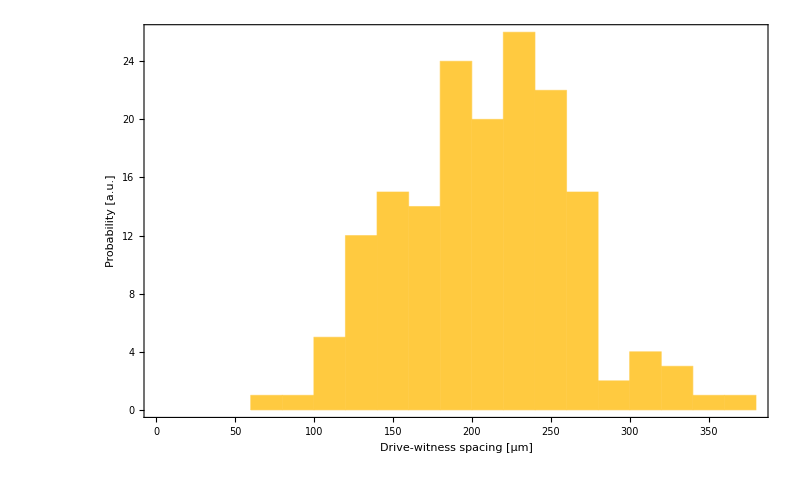

```mathematica
allSpacingValues = Table[
Median[allDriverData[[ii,All,"z"]]] - Median[allWitnessData[[ii,All,"z"]]],
{ii,Length[allDriverData]}
];

Histogram[10^6 allSpacingValues,
{20},
PlotRange->{{0,All},Automatic},
ImageSize->800,
Frame->True,
FrameLabel->{"Drive-witness spacing [μm]","Probability [a.u.]"},
LabelStyle->20
]
```

```mathematica
10^6 Median[allSpacingValues]
10^6 StandardDeviation[allSpacingValues]
```

212.658

54.4957

## Energy histogram

```mathematica
driverMedianEnergies = 10^-9 Median[#[[All,"pz"]]]&/@allDriverData;
witnessMedianEnergies = 10^-9 Median[#[[All,"pz"]]]&/@allWitnessData;
```

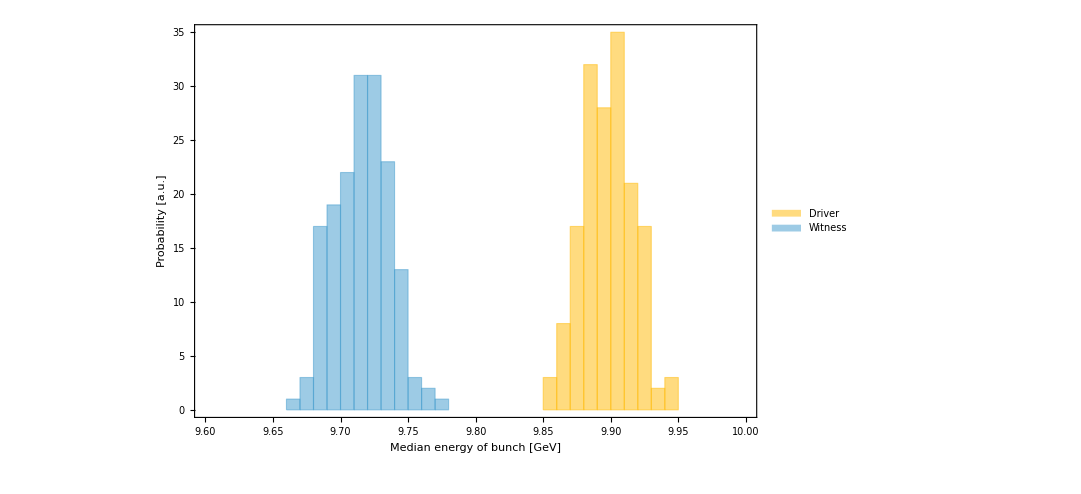

```mathematica
Histogram[{driverMedianEnergies,witnessMedianEnergies},
{0.01},
PlotRange->{{9.6,10.0},Automatic},
ImageSize->800,
Frame->True,
FrameLabel->{"Median energy of bunch [GeV]","Probability [a.u.]"},
LabelStyle->20,
ChartLegends->Placed[{"Driver","Witness"},{0.12,0.85}]
]
```

```mathematica
Median[driverMedianEnergies]
StandardDeviation[driverMedianEnergies]
```

9.89798

0.0189361

```mathematica
Median[witnessMedianEnergies]
StandardDeviation[witnessMedianEnergies]
```

9.71678

0.0199342

## Pointing

```mathematica
allDriverCentroids= {10^6 Median[#[[All,"x"]]],10^6 Median[#[[All,"y"]]]}&/@allDriverData;
allWitnessCentroids = {10^6 Median[#[[All,"x"]]],10^6 Median[#[[All,"y"]]]}&/@allWitnessData;
```

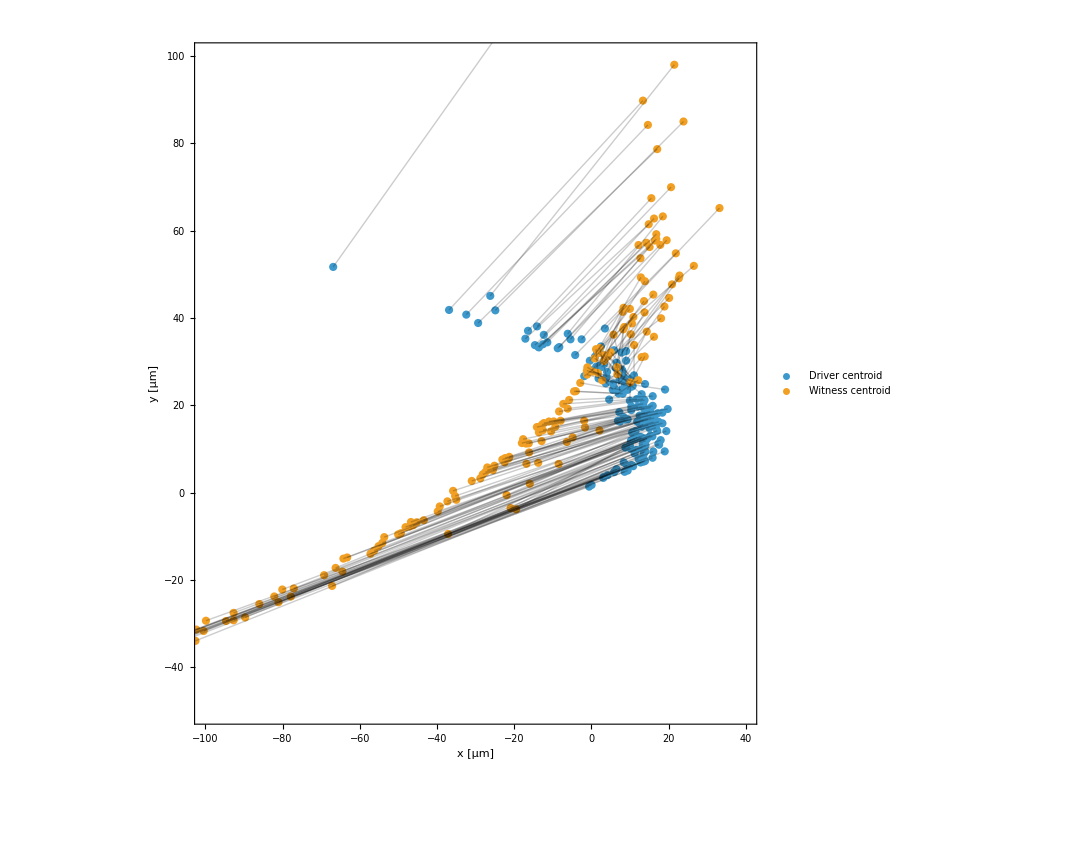

```mathematica
Show[
ListPlot[
{
allDriverCentroids,
allWitnessCentroids
},
PlotRange->{{-100,40},{-50,100}},
AspectRatio->Automatic,
Frame->True,
FrameLabel->{"x [μm]","y [μm]"},
LabelStyle->20,
ImageSize->800,
PlotLegends->{"Driver centroid","Witness centroid"}
],
Graphics[
{
Opacity[0.2],
Line[#]&/@Transpose[{allDriverCentroids,allWitnessCentroids}]
}
]
]
```

## Relative offsets

```mathematica
positionErrors = Table[
10^6 Norm[
{Median[allDriverData[[ii,All,"x"]]],Median[allDriverData[[ii,All,"y"]]]}-{Median[allWitnessData[[ii,All,"x"]]],Median[allWitnessData[[ii,All,"y"]]]}
],
{ii,Length[allDriverData]}
];

Median[positionErrors]
StandardDeviation[positionErrors]
```

34.5581

36.8097

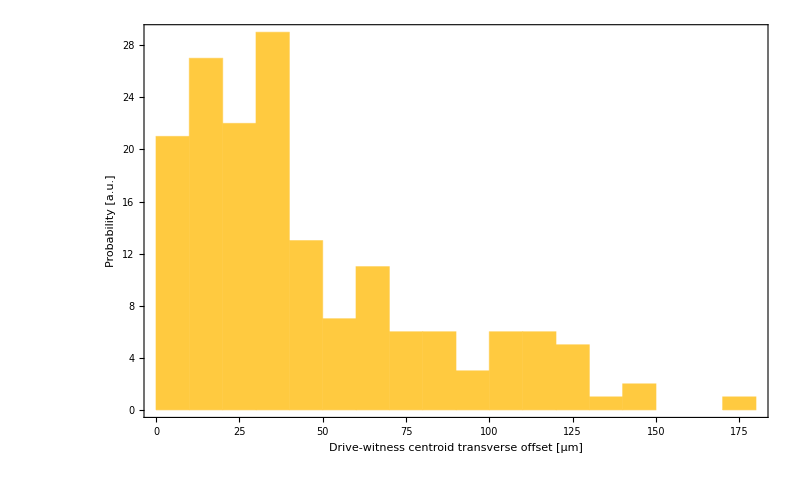

```mathematica
Histogram[positionErrors,
{10},
PlotRange->{{0,All},Automatic},
ImageSize->800,
Frame->True,
FrameLabel->{"Drive-witness centroid transverse offset [μm]","Probability [a.u.]"},
LabelStyle->20
]
```

```mathematica
angleErrors = Table[
10^6/(9.8*^9)Norm[
{Median[allDriverData[[ii,All,"px"]]],Median[allDriverData[[ii,All,"py"]]]}-{Median[allWitnessData[[ii,All,"px"]]],Median[allWitnessData[[ii,All,"py"]]]}
],
{ii,Length[allDriverData]}
];

Median[angleErrors]
StandardDeviation[angleErrors]
```

160.5

55.6802

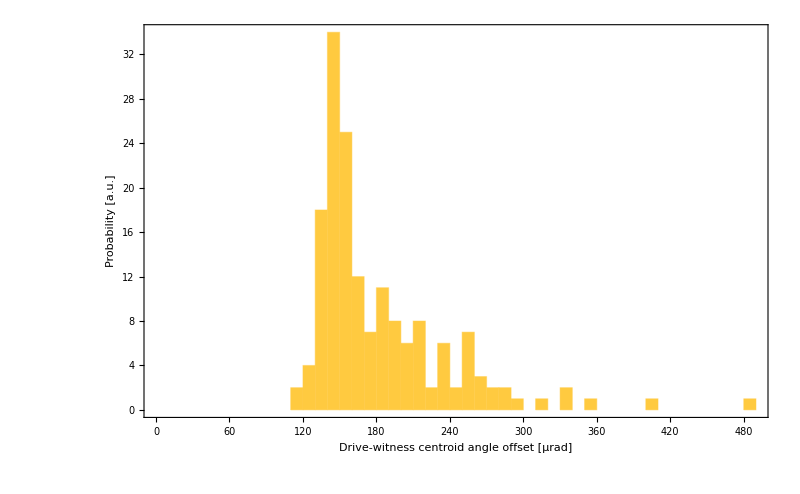

```mathematica
Histogram[angleErrors,
{10},
PlotRange->{{0,All},Automatic},
ImageSize->800,
Frame->True,
FrameLabel->{"Drive-witness centroid angle offset [μrad]","Probability [a.u.]"},
LabelStyle->20
]
```